```mathematica
Quit[]
```

```mathematica
δH=1;
MsSol=NSolve[{((2870/2.8)-XX/2)/2}==82+δH,XX][[1,1,2]]-4+2
```

1716.

```mathematica
(*-----------------------Paraunitary diagonalization-------------------------------------------------*)
Clear[ParaUnitaryDiag]
ParaUnitaryDiag[H_]:=Module[{Hdiag,T,K,Dim,σ3,W,esys,eval,evec,preperm,ordering,permutation,U,PhaseArrayP,PhaseArrayN,V,Tpp,Tpn,Tnp,Tnn},
K=CholeskyDecomposition[H];
Dim=Dimensions[H][[1]];
σ3=DiagonalMatrix[Table[(-1)^Floor[(2n-1)/Dim],{n,1,Dim}]];
W=K.σ3.ConjugateTranspose[K];
esys=Eigensystem[W];
eval=esys[[1]];
evec=Normalize/@esys[[2]];

preperm=Join[Table[Dim/2+n ,{n,1,Dim/2}],Table[Dim/2+1-n ,{n,1,Dim/2}]];
ordering=Ordering[eval];
permutation=PermutationProduct[preperm,ordering];(*make permutation that gives (+small,-small,+mid,-mid,+large,-large)*)

eval=eval[[permutation]];
evec=evec[[permutation]];
U=Transpose[evec];
Hdiag=σ3.DiagonalMatrix[eval];(* ConjugateTranspose[T].H.T*)
T=Inverse[K].U.Sqrt[Hdiag];(*There is degrees of freedom with T=>T*({{Exp[iΘ1], □, □, □, □, □}, {□, Exp[iΘ2], □, □, □, □}, {□, □, ..., □, □, □}, {□, □, □, Exp[-iψ1], □, □}, {□, □, □, □, Exp[-iψ2], □}, {□, □, □, □, □, ...}})*)
Tpp=T[[1;;Dim/2,1;;Dim/2]];(*Upper left*)
Tnn=T[[1+Dim/2;;Dim,1+Dim/2;;Dim]];(*Lower right*)
PhaseArrayP=Exp[I Arg[Diagonal[Tpp]]];
PhaseArrayN=Exp[I Arg[Diagonal[Tnn]]];
V=DiagonalMatrix[Flatten[Append[Conjugate[PhaseArrayP],Conjugate[PhaseArrayN]]]];
T=T.V;
Tpp=T[[1;;Dim/2,1;;Dim/2]];(*Upper left*)
Tnp=T[[1+Dim/2;;Dim,1;;Dim/2]];(*Lower left*)
Tpn=T[[1;;Dim/2,1+Dim/2;;Dim]];(*Upper right*)
Tnn=T[[1+Dim/2;;Dim,1+Dim/2;;Dim]];(*Lower right*)
{eval[[1;;Dim/2]],Tpp,Tnp,Tpn,Tnn,T}];


(*-------------------------material & condition parameters-----------------------------------------*)
Clear[M0,L,DD,γ,ωM]
M0=MsSol;(*Oe*)
L=3;(*μm*)
DD=5.4*10^-9*10^8;(*Oe μm^-2*)
γ=2.8*10^-3;(*GHz/G*)
ωM=γ*M0;(*GHz*)

(*-------------calculate dipolar exchange spin waves Hamiltonian-----------------------------------*)
Clear[F,P,Q,H,GenerateHBdG]
F[q_,n_]:=2*(1-(-1)^n Exp[-q])/q
P[q_,n_,m_]:=q^2/(q^2+n^2 π^2)KroneckerDelta[n,m]-1/(√((1+KroneckerDelta[n,0])(1+KroneckerDelta[m,0])))*q^4/((q^2+n^2 π^2)(q^2+m^2 π^2))F[q,n]*(1+(-1)^(n+m))/2
Q[q_,n_,m_]:=q^2/(q^2+m^2 π^2)(m^2/(m^2-n^2+(1+(-1)^(n+m))/2)2/q-q^2/(2(q^2+n^2 π^2))F[q,n])*1/(√((1+KroneckerDelta[n,0])(1+KroneckerDelta[m,0])))*(1-(-1)^(n+m))/2
Ω[ωH_,q_,n_]:=(ωH+ (γ*DD)/L^2(q^2+n^2 π^2))/ωM
H[ωH_,q_,ϕk_,n_,m_]:=(Ω[ωH,q,n]({{1, 0}, {0, 1}})+1/2({{1, 1}, {1, 1}}))*KroneckerDelta[n,m]-1/2({{1-(Sin[ϕk])^2, 1+(Sin[ϕk])^2}, {1+(Sin[ϕk])^2, 1-(Sin[ϕk])^2}})*P[q,n,m]-1/2({{0, -4}, {4, 0}})*Sin[ϕk]Q[q,n,m]
f[q_,n_,hoverL_]:=(-1)^n/(√(2(1+KroneckerDelta[n,0])))*q^2/(q^2+n^2 π^2)Exp[-q*hoverL]*(1-(-1)^n Exp[-q])

GenerateHBdG[ωH_,q_,ϕk_,Nmax_]:=Module[{HBdG,result,n,m},HBdG=Table[0,{n,1,2*Nmax},{m,1,2*Nmax}];
For[m=1,m≤Nmax,m++,
For [n=1,n≤Nmax,n++,
result=N[H[ωH,q,ϕk,n-1,m-1]];
HBdG[[n,m]]=result[[1,1]];
HBdG[[n,m+Nmax]]=result[[1,2]];
HBdG[[n+Nmax,m]]=result[[2,1]];
HBdG[[n+Nmax,m+Nmax]]=result[[2,2]];
]
];
HBdG
]

(*-------------execute the paraunitary diag & returns the interpolation function-----------------------------------*)
MultiParaDiag[hNVarray_,ωH_,qtable_,ϕtable_,Nmax_]:=
Module[{Numq,Numϕ,Measure,Qtable,Φtable,ωBdGtable,CouplingPlusTable,CouplingMinusTable,CouplingZTable,countq,countϕ,q,ϕk,HBdG,result,Tpp,Tpn,Tnp,Tnn,γplus,γplusMirror,γminus,γminusMirror,γz,γzMirror,NumhNV,fbarArray,vplusArray,vplusMirrorArray,vminusArray,vminusMirrorArray,vzArray,vzMirrorArray,IntωBdGtable,ϕtableMod,QtableExtend,ΦtableExtend,ωBdGtableExtend,CouplingPlusTableExtend,CouplingMinusTableExtend,CouplingZTableExtend,IntCouplingPlusTable,IntCouplingMinusTable,IntCouplingZTable},

Numq=Length[qtable];
Numϕ=Length[ϕtable];
NumhNV=Length[hNVarray];
Measure=Mean[Differences[qtable]]*Mean[Differences[ϕtable]]/(2π)^2;

(*Once calculating for ϕ, you're getting the result for ϕ+π as well. So the table size for ϕ is 2*Numϕ*)
Qtable=Table[qtable[[n]],{n,1,Numq},{m,1,2*Numϕ},{s,1,Nmax}];
Φtable=Table[ϕtable[[Mod[m-1,Numϕ]+1]]+π*(Ceiling[m/Numϕ]-1),{n,1,Numq},{m,1,2*Numϕ},{s,1,Nmax}];
ωBdGtable=Table[0,{n,1,Numq},{m,1,2*Numϕ},{s,1,Nmax}];
CouplingPlusTable=Table[0,{n,1,Numq},{m,1,2*Numϕ},{tt,1,NumhNV},{s,1,Nmax}];
CouplingMinusTable=Table[0,{n,1,Numq},{m,1,2*Numϕ},{tt,1,NumhNV},{s,1,Nmax}];
CouplingZTable=Table[0,{n,1,Numq},{m,1,2*Numϕ},{tt,1,NumhNV},{s,1,Nmax}];

Monitor[For[countq=1,countq≤Numq,countq++,
For[countϕ=1,countϕ≤Numϕ,countϕ++,
q=Qtable[[countq,countϕ,1]];
ϕk=Φtable[[countq,countϕ,1]];

HBdG=GenerateHBdG[ωH,q,ϕk,Nmax];
result=ParaUnitaryDiag[(HBdG+ConjugateTranspose[HBdG])/2];(*Para-diagonalization*)
ωBdGtable[[countq,countϕ]]=result[[1]];
ωBdGtable[[countq,countϕ+Numϕ]]=ωBdGtable[[countq,countϕ]];

Tpp=result[[2]];
Tnp=result[[3]];
Tpn=result[[4]];
Tnn=result[[5]];

γplus=(1+Sin[ϕk])/2(Tpp+Tnp+Sin[ϕk](Tpp-Tnp));
γplusMirror=(1+Sin[ϕk+π])/2 Conjugate[(Tnn+Tpn+Sin[ϕk+π](Tnn-Tpn))];
γminus=(1-Sin[ϕk])/2(Tpp+Tnp+Sin[ϕk](Tpp-Tnp));
γminusMirror=(1-Sin[ϕk+π])/2 Conjugate[(Tnn+Tpn+Sin[ϕk+π](Tnn-Tpn))];
γz=-I Cos[ϕk]/2(Tpp+Tnp+Sin[ϕk](Tpp-Tnp));
γzMirror=-I Cos[ϕk+π]/2 Conjugate[(Tnn+Tpn+Sin[ϕk+π](Tnn-Tpn))];

fbarArray=Table[f[q,nn-1,hNVarray[[tt]]/L],{tt,1,NumhNV},{nn,1,Nmax}];
vplusArray=Table[fbarArray[[tt,;;]].γplus,{tt,1,NumhNV}];
vplusMirrorArray=Table[fbarArray[[tt,;;]].γplusMirror,{tt,1,NumhNV}];
vminusArray=Table[fbarArray[[tt,;;]].γminus,{tt,1,NumhNV}];
vminusMirrorArray=Table[fbarArray[[tt,;;]].γminusMirror,{tt,1,NumhNV}];
vzArray=Table[fbarArray[[tt,;;]].γz,{tt,1,NumhNV}];
vzMirrorArray=Table[fbarArray[[tt,;;]].γzMirror,{tt,1,NumhNV}];

CouplingPlusTable[[countq,countϕ]]=vplusArray;
CouplingPlusTable[[countq,countϕ+Numϕ]]=vplusMirrorArray;
CouplingMinusTable[[countq,countϕ]]=vminusArray;
CouplingMinusTable[[countq,countϕ+Numϕ]]=vminusMirrorArray;
CouplingZTable[[countq,countϕ]]=vzArray;
CouplingZTable[[countq,countϕ+Numϕ]]=vzMirrorArray;
];
],Row[{ProgressIndicator[countq,{1,Numq}],N[100*countq/Numq]"% MultiParaDiag"}," "]];

(*For interpolation, append one point in the end that overlaps the initial ϕ*)
QtableExtend=Table[qtable[[n]],{n,1,Numq},{m,1,2*Numϕ+1},{s,1,Nmax}];
ΦtableExtend=Table[ϕtable[[Mod[m-1,Numϕ]+1]]+π*(Ceiling[m/Numϕ]-1),{n,1,Numq},{m,1,2*Numϕ+1},{s,1,Nmax}];
ωBdGtableExtend=Table[0,{n,1,Numq},{m,1,2*Numϕ+1},{s,1,Nmax}];
CouplingPlusTableExtend=Table[0,{n,1,Numq},{m,1,2*Numϕ+1},{tt,1,NumhNV},{s,1,Nmax}];
CouplingMinusTableExtend=Table[0,{n,1,Numq},{m,1,2*Numϕ+1},{tt,1,NumhNV},{s,1,Nmax}];
CouplingZTableExtend=Table[0,{n,1,Numq},{m,1,2*Numϕ+1},{tt,1,NumhNV},{s,1,Nmax}];

For[countq=1,countq≤Numq,countq++,
For[countϕ=1,countϕ≤2Numϕ,countϕ++,
ωBdGtableExtend[[countq,countϕ]]=ωBdGtable[[countq,countϕ]];
CouplingPlusTableExtend[[countq,countϕ]]=CouplingPlusTable[[countq,countϕ]];
CouplingMinusTableExtend[[countq,countϕ]]=CouplingMinusTable[[countq,countϕ]];
CouplingZTableExtend[[countq,countϕ]]=CouplingZTable[[countq,countϕ]];
];
ωBdGtableExtend[[countq,2*Numϕ+1]]=ωBdGtable[[countq,1]];
CouplingPlusTableExtend[[countq,2*Numϕ+1]]=CouplingPlusTable[[countq,1]];
CouplingMinusTableExtend[[countq,2*Numϕ+1]]=CouplingMinusTable[[countq,1]];
CouplingZTableExtend[[countq,2*Numϕ+1]]=CouplingZTable[[countq,1]];
];

ϕtableMod=Table[Φtable[[1,n,1]],{n,1,2*Numϕ}];
IntωBdGtable=Table[Interpolation[Transpose[{Transpose[{Flatten[QtableExtend[[;;,;;,s]]],Flatten[ΦtableExtend[[;;,;;,s]]]}],Flatten[ωBdGtableExtend[[;;,;;,s]]]}],InterpolationOrder->2],{s,1,Nmax}];
IntCouplingPlusTable=Table[Interpolation[Transpose[{Transpose[{Flatten[QtableExtend[[;;,;;,s]]],Flatten[ΦtableExtend[[;;,;;,s]]]}],Flatten[CouplingPlusTableExtend[[;;,;;,tt,s]]]}],InterpolationOrder->2],{tt,1,NumhNV},{s,1,Nmax}];
IntCouplingMinusTable=Table[Interpolation[Transpose[{Transpose[{Flatten[QtableExtend[[;;,;;,s]]],Flatten[ΦtableExtend[[;;,;;,s]]]}],Flatten[CouplingMinusTableExtend[[;;,;;,tt,s]]]}],InterpolationOrder->2],{tt,1,NumhNV},{s,1,Nmax}];
IntCouplingZTable=Table[Interpolation[Transpose[{Transpose[{Flatten[QtableExtend[[;;,;;,s]]],Flatten[ΦtableExtend[[;;,;;,s]]]}],Flatten[CouplingZTableExtend[[;;,;;,tt,s]]]}],InterpolationOrder->2],{tt,1,NumhNV},{s,1,Nmax}];

{qtable,Min[ωBdGtable],ϕtableMod,IntωBdGtable,IntCouplingPlusTable,IntCouplingMinusTable,IntCouplingZTable}(*ωBdGtable,CouplingPlusTable,CouplingMinusTable,CouplingZTable,Measure*)
]
```

```mathematica
(*------------------For Γ1 calculations-----------------*)
(*-----can make it big-------------*)
Numϕ=2*90;
NumQ=2*10;
(*--------------------------------*)
Delϕ=π/Numϕ;
ϕtable=Table[ϕ,{ϕ,0,π-Delϕ,Delϕ}];
Qmax=50*L;(*till 50 rad/μm*)
(*DelQ=Qmax/NumQ;*)
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
qtable=N[Join[{10^-6},fSpace[L/1000,Qmax,NumQ]]];
(*qtable=N[Join[{10^-6},Table[n,{n,DelQ,Qmax,DelQ}]]];*)
Fmax=5;
Nmax=Ceiling[L/π √(Fmax/(γ DD))];(*till 5GHz*)
(*Print["Nmax is ",Nmax]*)

(*Set Temperature*)
hPlank=6.626*10^-34;(*J*s*)
μ0=4π*10^-7;(*H/m*)
ωd=(hPlank*μ0*(γ*10^9)^2/(L*10^-6)^3)*10^8;(*Hz*)
kB=1.381*10^-23;(*J/K*)
Temperature=300;(*K*)
NBose[ω_]:=(10^-9*kB*Temperature/hPlank)/ω;
(*1/(Exp[ω/(10^-9*kB*Temperature/hPlank)]-1)*)
(*(10^-9*kB*Temperature/hPlank)/ω*)

(*Define module to calculate ΓPlus and ΓMinus*)
Clear[ΓValuesUL]
ΓValuesUL[ηsmall_,NQest_,NΦ_,H0_,IntωBdGtable_,IntCouplingPlusTable_,IntCouplingMinusTable_,NumhNV_]:=Module[{DNV,ωtargetL,ωtargetU,Qmiddle,NQhalf,Qtable,LastδQ,δQ,NQ,δΦ,FlatQtable,FlatδQtable,FlatΦtable,FlatωBdGtable,FlatCouplingPlusTableArray,FlatCouplingMinusTableArray,LengthFlatTable,s,ii,ΓLHzArray,ΓUHzArray,DOSL,DOSU},
DNV=2.87;
ωtargetL=DNV-H0*γ;ωtargetU=DNV+H0*γ;
Qmiddle=5L;
NQhalf=Round[NQest/2];
Qtable=N[Join[{10^-6},fSpace[L/1000,Qmiddle,NQhalf]]];(*NQ+1 elements*)
LastδQ=Differences[Qtable][[Length[Qtable]-1]];
Qtable=Join[Qtable,Range[Max[Qtable]+LastδQ,Qmax,LastδQ]];

δQ=Differences[Qtable];(*NQ elements*)
NQ=Length[δQ];
δΦ=2π/NΦ;
ΓLHzArray=Table[0,{tt,1,NumhNV}];ΓUHzArray=Table[0,{tt,1,NumhNV}];DOSL=0;DOSU=0;

Monitor[For[s=1,s≤ Nmax,s++,
FlatQtable=Flatten[Table[Qtable[[ii1]],{ii1,1,NQ},{ii2,1,NΦ}]];
FlatδQtable=Flatten[Table[δQ[[ii1]],{ii1,1,NQ},{ii2,1,NΦ}]];
FlatΦtable=Flatten[Table[2π*(ii2-1)/NΦ,{ii1,1,NQ},{ii2,1,NΦ}]];
FlatωBdGtable=Flatten[Table[0,{ii1,1,NQ},{ii2,1,NΦ}]];
FlatCouplingPlusTableArray=Table[Flatten[Table[0,{ii1,1,NQ},{ii2,1,NΦ}]],{tt,1,NumhNV}];
FlatCouplingMinusTableArray=Table[Flatten[Table[0,{ii1,1,NQ},{ii2,1,NΦ}]],{tt,1,NumhNV}];
LengthFlatTable=Length[FlatωBdGtable];

For[ii=1,ii≤ LengthFlatTable,ii++,
FlatωBdGtable[[ii]]=IntωBdGtable[[s]][FlatQtable[[ii]],FlatΦtable[[ii]]];
FlatCouplingPlusTableArray[[;;,ii]]=Table[IntCouplingPlusTable[[tt,s]][FlatQtable[[ii]],FlatΦtable[[ii]]],{tt,1,NumhNV}];
FlatCouplingMinusTableArray[[;;,ii]]=Table[IntCouplingMinusTable[[tt,s]][FlatQtable[[ii]],FlatΦtable[[ii]]],{tt,1,NumhNV}];
];

DOSL=DOSL+(1/L^2)*(δΦ/(2π)^2)*Sum[FlatδQtable[[jj]]*FlatQtable[[jj]]*(ηsmall/π)/(ηsmall^2+(ωM*FlatωBdGtable[[jj]]-ωtargetL)^2),{jj,1,LengthFlatTable}];
DOSU=DOSU+(1/L^2)*(δΦ/(2π)^2)*Sum[FlatδQtable[[jj]]*FlatQtable[[jj]]*(ηsmall/π)/(ηsmall^2+(ωM*FlatωBdGtable[[jj]]-ωtargetU)^2),{jj,1,LengthFlatTable}];
ΓLHzArray=ΓLHzArray+(2π)^2*ωM*ωd*(δΦ/(2π)^2)*Sum[(2NBose[ωM*FlatωBdGtable[[jj]]]+1)*FlatδQtable[[jj]]*FlatQtable[[jj]]*(Abs[FlatCouplingPlusTableArray[[;;,jj]]])^2*(ηsmall/π)/(ηsmall^2+(ωM*FlatωBdGtable[[jj]]-ωtargetL)^2),{jj,1,LengthFlatTable}];
ΓUHzArray=ΓUHzArray+(2π)^2*ωM*ωd*(δΦ/(2π)^2)*Sum[(2NBose[ωM*FlatωBdGtable[[jj]]]+1)*FlatδQtable[[jj]]*FlatQtable[[jj]]*(Abs[FlatCouplingMinusTableArray[[;;,jj]]])^2*(ηsmall/π)/(ηsmall^2+(ωM*FlatωBdGtable[[jj]]-ωtargetU)^2),{jj,1,LengthFlatTable}];
],Row[{ProgressIndicator[s,{1,Nmax}],"performing s=",s," calculation: ",N[100*s/Nmax]" % Γ1Calc"}]];
{DOSL,DOSU,ΓLHzArray,ΓUHzArray}
]

hNVarray={0.4,0.5,0.6,0.7};(*pos of NV in um*)

Clear[Γ1FromH0]
Γ1FromH0[H0_]:=Module[{ωH,result,qtableTemp,ωMin,ϕtableMod,IntωBdGtable,IntCouplingPlusTable,IntCouplingMinusTable,IntCouplingZTable,ηsmall,NQ,NΦ,DOSL,DOSU,ΓLHzArray,ΓUHzArray},
(*H0=200;(*360;*)(*Oe*)*)
ωH=γ*H0;(*GHz*)
(*hNVarray={0.8};(*pos of NV in um*)*)
result=MultiParaDiag[hNVarray,ωH,qtable,ϕtable,Nmax];
{qtableTemp,ωMin,ϕtableMod,IntωBdGtable,IntCouplingPlusTable,IntCouplingMinusTable,IntCouplingZTable}=result;
ηsmall=0.003;
NQ=2*10;NΦ=2*360;
{DOSL,DOSU,ΓLHzArray,ΓUHzArray}=ΓValuesUL[ηsmall,NQ,NΦ,H0,IntωBdGtable,IntCouplingPlusTable,IntCouplingMinusTable,Length[hNVarray]];
(*Print["DOS(ω=ωL)=", DOSL, " 1/GHz μm^2"]
Print["DOS(ω=ωU)=", DOSU, " 1/GHz μm^2"]*)
Print["Γ(ω=ωL)=", ΓLHz, " Hz"];
Print["Γ(ω=ωU)=", ΓUHz, " Hz"]
{DOSL,DOSU,ΓLHzArray,ΓUHzArray}
]
```

```mathematica
(2NBose[2.8]+1)
Coth[1/((10^-9*kB*Temperature/hPlank)/(2.8))]
```

4467.17

2233.09

```mathematica
H0Array={82}(*{76,77,78,79,80,81,81.5,82,82.5,83,84,85,86,87,88,89,90,91,92,95}
DOSLarray=0*H0Array;DOSUarray=0*H0Array;*)
ΓLHzArray=Table[0*H0Array,{tt,1,Length[hNVarray]}];ΓUHzArray=Table[0*H0Array,{tt,1,Length[hNVarray]}];
```

{82}

```mathematica
Γ1FromH0[82]
```

Γ(ω=ωL)=ΓLHz Hz

Γ(ω=ωU)=ΓUHz Hz

{1206.77 Null,1501.43 Null,{277072. Null,175966. Null,115688. Null,77320.5 Null},{7.70728 Null,2.15139 Null,0.917334 Null,0.539083 Null}}

```mathematica
Niteration=Length[H0Array];
Monitor[For[ii=1,ii≤Niteration,ii++,
resultΓUL=Γ1FromH0[H0Array[[ii]]];
DOSLarray[[ii]]=resultΓUL[[1]];
DOSUarray[[ii]]=resultΓUL[[2]];
ΓLHzArray[[;;,ii]]=resultΓUL[[3]];
ΓUHzArray[[;;,ii]]=resultΓUL[[4]];
],Row[{ProgressIndicator[ii,{1,Niteration}],"Now at H0=",H0Array[[ii]],": ",N[100*ii/Niteration]" %"}]];
```

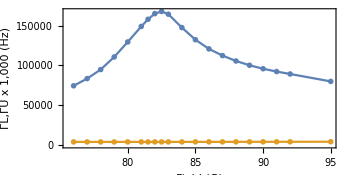

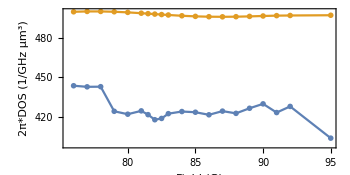

```mathematica
ShowhNVIndex=1;
ListPlot[{Transpose[{H0Array,ΓLHzArray[[ShowhNVIndex,;;]]}],Transpose[{H0Array,ΓUHzArray[[ShowhNVIndex,;;]]*1000}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "ΓL,ΓU x 1,000 (Hz)"},Joined->True,PlotMarkers->{"∘",30}]
ListPlot[{Transpose[{H0Array,DOSLarray/(L)}],Transpose[{H0Array,DOSUarray/(L)}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "2π*DOS (1/GHz μm^3)"},Joined->True,PlotMarkers->{"∘",30}]
```

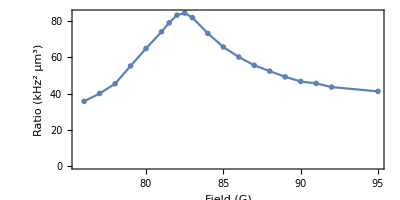

```mathematica
Ratio=H0Array*0;
For[ii=1,ii≤ Niteration,ii++,
If[DOSLarray[[ii]]>0,Ratio[[ii]]=(10^-3*ΓLHzArray[[ShowhNVIndex,ii]]*L)/(10^-6*DOSLarray[[ii]]*2NBose[2.87-γ*H0Array[[ii]]])](*Unit: kHz^2 μm^3*)
]
ListPlot[{Transpose[{H0Array,Ratio}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "Ratio (kHz^2 μm^3)"},Joined->True,PlotMarkers->{"∘",30},PlotRange->All]
```

```mathematica
(*Export["Desktop//Magnon_NV_FieldDep refined//19//19_T1FieldDep_MultiplehNV_JointLogLinearIntegral_nonlinearB.wdx",{H0Array,DOSLarray,DOSUarray,hNVarray,ΓLHzArray,ΓUHzArray}];*)
```

```mathematica
{H0Array,DOSLarray,DOSUarray,hNVarray,ΓLHzArray,ΓUHzArray}=Import["Desktop//Magnon_NV_FieldDep refined//19//19_T1FieldDep_MultiplehNV_JointLogLinearIntegral_nonlinearB.wdx"];
```

```mathematica
(*(*Need to divided by L for the density of states 2πρ*)*)
```

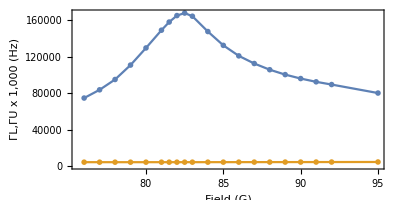

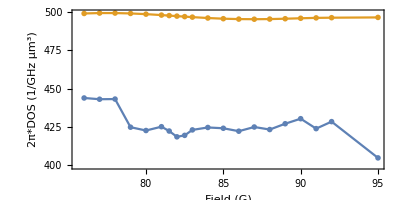

```mathematica
ShowhNVIndex=1;
ListPlot[{Transpose[{H0Array,ΓLHzArray[[ShowhNVIndex,;;]]}],Transpose[{H0Array,ΓUHzArray[[ShowhNVIndex,;;]]*1000}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "ΓL,ΓU x 1,000 (Hz)"},Joined->True,PlotMarkers->{"∘",30}]
ListPlot[{Transpose[{H0Array,DOSLarray/(L)}],Transpose[{H0Array,DOSUarray/(L)}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "2π*DOS (1/GHz μm^3)"},Joined->True,PlotMarkers->{"∘",30}]
```

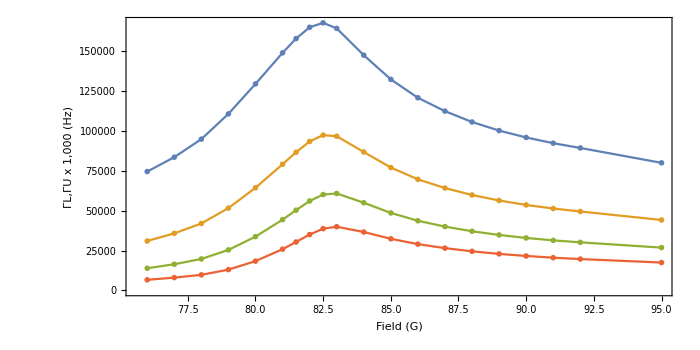

```mathematica
ListPlot[{Transpose[{H0Array,ΓLHzArray[[1,;;]]}],Transpose[{H0Array,ΓLHzArray[[2,;;]]}],Transpose[{H0Array,ΓLHzArray[[3,;;]]}],Transpose[{H0Array,ΓLHzArray[[4,;;]]}]},Frame->True,PlotRange->All,AspectRatio->1/2,FrameLabel->{"Field (G)", "ΓL,ΓU x 1,000 (Hz)"},Joined->True,PlotMarkers->{"∘",30},ImageSize->700]
```

```mathematica
(*Save as dat file*)
SavingMatrix=Join[{Join[{0},H0Array]},Transpose[Join[{hNVarray},Transpose[ΓLHzArray]]]];
```

```mathematica
(*Export["Desktop//Magnon_NV_FieldDep refined//19//19_T1FieldDep_MultiplehNV_JointLogLinearIntegral_nonlinearB.dat",SavingMatrix]*)
```

Desktop//Magnon_NV_FieldDep refined//19//19_T1FieldDep_MultiplehNV_JointLogLinearIntegral_nonlinearB.dat